```mathematica
(* Set machine precision *)
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`30."&);
```

```mathematica
DihedralMat[θ12_,θ13_,θ14_,θ23_,θ24_,θ34_]:=
{{-1,Cos[θ34],Cos[θ24],Cos[θ23]},
{Cos[θ34],-1,Cos[θ14],Cos[θ13]},
{Cos[θ24],Cos[θ14],-1,Cos[θ12]},
{Cos[θ23],Cos[θ13],Cos[θ12],-1}};
```

```mathematica
ModifiedMat[θ12_,θ13_,θ14_,θ23_,θ24_,θ34_]:=Module[{mat,newmat},
mat=DihedralMat[θ12,θ13,θ14,θ23,θ24,θ34];
newmat=Transpose[
{mat[[All,1]],
Sin[θ12]mat[[All,2]]+Sin[θ13]mat[[All,3]]+Sin[θ14]mat[[All,4]]}
];
Return[newmat];
]
```

```mathematica
GenerateCases:=
Module[{θ12,θ13,θ14,mat,det1, det2, det3,minimum,
cases={},noncases={},msg,examinedcnt=0,remaincnt=0,nonzerot=10^-3, smallestnonzero=∞},
(* Iterate through θ23, θ24, θ34
Tiling assumption: θ23, θ24, θ34 are of the form 2Pi/(2n)
Isoperimetric assumption: θ23, θ24, θ34 are at least 36.5 degrees
Nondegeneracy assumption: θ23, θ24, θ34 cannot be all Pi/2
*)
Do[ 
Do[
Do[
If[θ23==θ24==θ34==Pi/2,Continue[];];
(*
Isoperimetric assumption: n12 + n13 + n14 ≤ 9,
Combinatorial assumption: n12, n13, n14 have the same parity,
Nondegeneracy assumption: at most one of n12, n13, n14 is zero,
Symmetry assumption: n12 ≤ n13 ≤ n14, if n12 = n13 then θ24 ≥ θ34,
if n13 = n14 then θ23 ≥ θ24
*)
For[n12=0, n12≤ 9, n12++,
For[n13=1, n13≤ 9, n13++,
For[n14=1, n14≤ 9, n14++,
(*Enforce this condition to get rid of duplicate cases through symmetry*)
If[!(n12≤n13≤n14),Continue[];];
If[n12==n13&&θ24<θ34,Continue[];];
If[n13==n14&&θ23<θ24,Continue[];];
(*The sum of the number of angles should be less than or equal to 9*)
If[n12+n13+n14>9,Continue[];];
(*The number of angles is either all even or all odd*)
If[!(EvenQ[n12]==EvenQ[n13]==EvenQ[n14]),
Continue[];];

examinedcnt++;

θ14=(2Pi-n12 θ12-n13 θ13)/n14;
mat=ModifiedMat[θ12,θ13,θ14,θ23,θ24,θ34];
det1=mat[[{1,2}]]//Det;
det2=mat[[{1,3}]]//Det;
det3=mat[[{1,4}]]//Det;

Print[det1^2+det2^2+det3^2,Reduce[Pi/180*36.5<θ12<4 Pi/5&&
Pi/180*36.5<θ13<4 Pi/5&&
Pi/180*36.5<θ14<4 Pi/5&&
θ12+θ13+θ14>Pi&&
θ12+θ23+θ24>Pi&&
θ13+θ23+θ34>Pi&&
θ14+θ24+θ34>Pi&&
θ12+θ34+θ13+θ24<2Pi&&
θ12+θ34+θ14+θ23<2Pi&&
θ13+θ24+θ14+θ23<2Pi, {θ12,θ13}]];

minimum=NMinimize[{
det1^2+det2^2+det3^2,
Pi/180*36.5<θ12<4 Pi/5&&
Pi/180*36.5<θ13<4 Pi/5&&
Pi/180*36.5<θ14<4 Pi/5&&
θ12+θ13+θ14>Pi&&
θ12+θ23+θ24>Pi&&
θ13+θ23+θ34>Pi&&
θ14+θ24+θ34>Pi&&
θ12+θ34+θ13+θ24<2Pi&&
θ12+θ34+θ14+θ23<2Pi&&
θ13+θ24+θ14+θ23<2Pi},
 {θ12,θ13},
Method->{"RandomSearch","SearchPoints"->10,"RandomSeed"->0},
WorkingPrecision->30];

Clear[θ12,θ13,θ14];

(* Ignore if minimum is greather than zero *)
If[Abs[minimum[[1]]]>nonzerot,
AppendTo[noncases,{θ23,θ24,θ34,n12,n13,n14,minimum[[1]],minimum[[2]]}];
smallestnonzero=Min[smallestnonzero,minimum[[1]]];
Continue[];,

Print["θ23=",θ23," θ24=",θ24," θ34=", θ34," n12=",n12," n13=",n13," n14=",n14," mininum=",minimum];
AppendTo[cases,{θ23,θ24,θ34,n12,n13,n14,minimum[[1]],minimum[[2]]}];
remaincnt++;
];
]
]
],
{θ34,{Pi/2,Pi/3,Pi/4 }}],
{θ24,{Pi/2,Pi/3 ,Pi/4 }}],
{θ23,{Pi/2,Pi/3 ,Pi/4 }}];
msg="Examined "<>ToString[examinedcnt]<>" cases."
<>"\nSmallest nonzero minimum is "<>ToString[smallestnonzero]<>"."
<>"\n"<>ToString[remaincnt]<>" cases remain.";
Print[msg];
Return[{noncases,cases,msg}];
]
```

```mathematica
(* Generate cases from scratch *)
{noncases,cases,generatemsg}=GenerateCases;
```

```mathematica
(* These are precomputed *)
cases={{π/2,π/3,π/4,0,2,2,5.73952561144274089427172296428704436491383852513399915473505108417`30.*^-31,{θ12$1933->0.7227342478134149619568596407765600952967699904356966458872`30.,θ13$1933->1.209429202888188090932838403195440129646971560165083996829`30.}},{π/2,π/4,π/4,0,2,2,7.97831904776683694846843063420671181883975761330511346239362143191`30.*^-31,{θ12$1933->1.0471975511965971799249687730073268990437806197493824945221`30.,θ13$1933->1.0471975511965971367081413744957424104882183795803091108006`30.}},{π/3,π/2,π/4,1,1,3,1.379731061101417494597514761685444785018284036543921570128587100505`30.*^-30,{θ12$1933->0.7227342478134164430335999216905113750116845286548967255736`30.,θ13$1933->1.9321634507016032531057987347054944952512536218461454183472`30.}},{π/3,π/4,π/2,0,2,4,1.892209657260512540690817868310595580037439890743032431635917477761`30.*^-30,{θ12$1933->1.9321634507016033449011883905135968501640169189215881593779`30.,θ13$1933->0.7227342478134163231251264586348960973605591586967704240826`30.}},{π/4,π/2,π/4,1,1,3,2.05092720389901837861791675453199803951314179109572998880505787951`30.*^-30,{θ12$1933->1.0471975511965979909665493160531390621819133767745532094693`30.,θ13$1933->2.0943951023931943943906126641541852772421860148684883730936`30.}},{π/4,π/4,π/2,0,2,4,2.520774577452561205643932057556749399307533164769881031826061460264`30.*^-30,{θ12$1933->2.094395102393194384697283306634279100762770987906791142017`30.,θ13$1933->1.047197551196598108645728029371440208517708049266068282019`30.}},{π/4,π/4,π/3,0,2,2,3.206314180279995512243607496437855848256325410937334301703298193344`30.*^-30,{θ12$1933->1.9106332362490176012894064293436540622067763906233610925198`30.,θ13$1933->1.5707963267948958336668561014808151192059667798807480263939`30.}}};
```

```mathematica
EliminateCases[cases_]:=Module[{θ23,θ24,θ34,n12,n13,n14,θ12,θ13,θ14,mat,det1,det2,det3,expr,solution,
θ12solved,θ13solved,θ14solved,bad,msg,eliminatedcases={},remainedcases={},examinedcnt=0,remaincnt=0},
Do[
{θ23,θ24,θ34,n12,n13,n14,_,_}=case;
Print["θ23=",θ23," θ24=",θ24," θ34=",θ34," n12=",n12," n13=",n13," n14=",n14 ];

examinedcnt++;

θ14=(2Pi- n12 θ12-n13 θ13)/n14;

mat=ModifiedMat[θ12, θ13, θ14, θ23, θ24, θ34];
det1=mat[[{1,2}]]//Det//FullSimplify;
det2=mat[[{1,3}]]//Det//FullSimplify;
det3=mat[[{1,4}]]//Det //FullSimplify;

expr=det1==0&&
det2==0&&
det3==0&&
Pi/5<θ12<4Pi/5&&
Pi/5<θ13<4Pi/5&&
Pi/5<θ14<4Pi/5&&
θ12+θ13+θ14>Pi&&
θ12+θ23+θ24>Pi&&
θ13+θ23+θ34>Pi&&
θ14+θ24+θ34>Pi&&
θ12+θ34+θ13+θ24<2Pi&&
θ12+θ34+θ14+θ23<2Pi&&
θ13+θ24+θ14+θ23<2Pi;

solution=Solve[expr,{θ12,θ13}];

Clear[θ12,θ13,θ14];

If[MatchQ[solution,_Solve],
solution="Can't solve";
];

solution =solution//FullSimplify;

Print["Solution: ", solution];

bad=False;

If[solution=={},
bad=True;
msg="Eliminated because there is no solution.";
];

If[Length[solution]==1,
θ12solved=Normal[θ12/.solution[[1]]];
θ13solved=Normal[θ13/.solution[[1]]];
θ14solved=(2Pi-n12 θ12solved-n13 θ13solved)/n14 ;

Print["θ12=",θ12solved," θ13=",θ13solved," θ14=",θ14solved];

If[Element[2Pi/θ12solved,Integers]&&
Element[2Pi/θ13solved,Integers]&&
Element[2Pi/θ14solved,Integers],
bad=True;
msg="Eliminated because all dihedral angles are of the form 2pi/n.";
];
];

If[bad,
Print[msg];
AppendTo[eliminatedcases,{θ23,θ24,θ34,n12,n13,n14,solution,msg}],

AppendTo[remainedcases,{θ23,θ24,θ34,n12,n13,n14,solution}];
remaincnt++;
];,
{case,cases}];
Print["Examined ",examinedcnt," cases."];
Print[remaincnt," cases remain."];
Return[{eliminatedcases,remainedcases}];
]
```

```mathematica
(* Run case elimination *)
{eliminatedcases,remainedcases}=EliminateCases[cases]
```

```mathematica
(* This is precomputed *)
eliminatedcases={{π/2,π/4,π/4,0,2,2,{{θ12->π/3,θ13->π/3}},"Eliminated because all dihedral angles are of the form 2pi/n."},{π/3,π/4,π/2,0,2,4,{},"Eliminated because there is no solution."},{π/4,π/4,π/2,0,2,4,{{θ12->(2 π)/3,θ13->π/3}},"Eliminated because all dihedral angles are of the form 2pi/n."}};
```

```mathematica
(* This is precomputed *)
remainedcases={{π/2,π/3,π/4,0,2,2,{{θ12->4 ArcCot[2 √2+√7],θ13->1/2 (π-4 ArcCot[2 √2+√7])}}},{π/3,π/2,π/4,1,1,3,"Can't solve"},{π/4,π/2,π/4,1,1,3,"Can't solve"},{π/4,π/4,π/3,0,2,2,"Can't solve"}};
```

```mathematica
IntervalMinimize[(-Cos[1/2 (2 π-2 θ13$5320)] Sin[θ12$5320]-Cos[θ12$5320] Sin[1/2 (2 π-2 θ13$5320)]+Sin[θ13$5320])^2+(-Cos[θ13$5320] Sin[θ12$5320]+Sin[1/2 (2 π-2 θ13$5320)]-Cos[θ12$5320] Sin[θ13$5320])^2+((3 Sin[θ12$5320])/4-Cos[θ13$5320] Sin[1/2 (2 π-2 θ13$5320)]-Cos[1/2 (2 π-2 θ13$5320)] Sin[θ13$5320])^2]
```

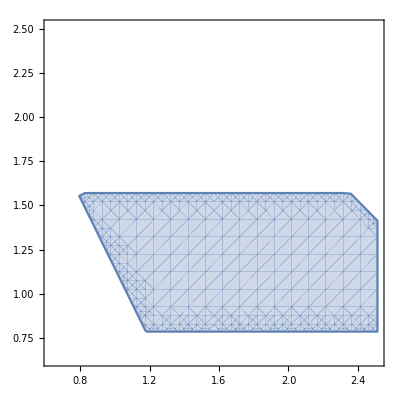

```mathematica
RegionPlot[(0.7853981633974483<θ12$13248≤1.1780972450961724&&3.141592653589793-2. θ12$13248<θ13$13248<1.5707963267948966)||(1.1780972450961724<θ12$13248≤2.356194490192345&&0.7853981633974483<θ13$13248<1.5707963267948966)||(2.356194490192345<θ12$13248<2.5132741228718345&&0.7853981633974483<θ13$13248<0.25 (15.707963267948966-4. θ12$13248)),{θ12$13248,Pi/5, 4Pi/5},{θ13$13248,Pi/5, 4Pi/5}]
```

```mathematica
const=FullSimplify[(0.7853981633974483<θ12$13248≤1.1780972450961724&&3.141592653589793-2. θ12$13248<θ13$13248<1.5707963267948966)||(1.1780972450961724<θ12$13248≤2.356194490192345&&0.7853981633974483<θ13$13248<1.5707963267948966)||(2.356194490192345<θ12$13248<2.5132741228718345&&0.7853981633974483<θ13$13248<0.25 (15.707963267948966-4. θ12$13248))]
```

(θ12$13248≤1.1781&&3.14159-2. θ12$13248<θ13$13248<1.5708)||(1.1781<θ12$13248≤2.35619&&0.785398<θ13$13248<1.5708)||(2.35619<θ12$13248<2.51327&&0.785398<θ13$13248<3.92699-1. θ12$13248)

```mathematica
First/@{Minimize[{θ12$13248,const},{θ12$13248,θ13$13248}],Maximize[{θ12$13248,const},{θ12$13248,θ13$13248}]}
First/@{Minimize[{θ13$13248,const},{θ12$13248,θ13$13248}],Maximize[{θ13$13248,const},{θ12$13248,θ13$13248}]}
```

{0.785398,2.51327}

{0.785398,1.5708}